# The Size of Eden Clusters

## Milan Cvitkovic

## Section 01: Introduction

In this notebook we will attempt to determine a formula for how the number of particles (sites) in an Eden model cluster (n) depends on the radius of gyration of the cluster (r).  We will assume that n is given by n = c*r^d - taking the log of both sides of this equation gives log[n] = log[c]+d*log[r], showing that if we keep track of n and r and found a linear fit it would give us values for log[c] and d as the intercept and slope, respectively.  We will develop code to simulate Eden growth and grow a cluster of a certain size, find the radius of gyration of that cluster, run a number of simulations and find r and n for a number of clusters, and use the radii and cluster sizes from these simulations to find good average values for Log[c] and d.

## Section 02: Needed Packages

None.

## Section 03: Some Needed Statistical Functions

```mathematica
Clear[ave, aveSqr, var, unc]
ave[List_] := N[Apply[Plus,List]/Length[List]];
aveSqr[List_] := N[Apply[Plus,List^2]/Length[List]];
var[List_] := aveSqr[List]-ave[List]^2;
unc[List_] := Sqrt[var[List]/Length[List]]
```

Testing code:

```mathematica
Clear[TestList,a,b,c,d]
TestList = {a,b,c,d}
ave[TestList]
aveSqr[TestList]
var[TestList]
unc[TestList]
```

{a,b,c,d}

0.25 (a+b+c+d)

0.25 (a^2+b^2+c^2+d^2)

-0.0625 (a+b+c+d)^2+0.25 (a^2+b^2+c^2+d^2)

1/2 √(-0.0625 (a+b+c+d)^2+0.25 (a^2+b^2+c^2+d^2))

The symbolic interpretations are correct - all seem to work correctly.

## Section 04: The eden03[] Module

```mathematica
Clear[eden03]
eden03[n_]:=
Module[
{choices,findNewCluster03,newSite,newBorder},

choices={{1,0},{0,1},{-1,0},{0,-1}};

findNewCluster03:=
(
newSite=#[[2,RandomInteger[{1,Length[#[[2]]]}]]];
newBorder =Complement[Union[#[[2]],Map[(#+newSite)&,choices]],{newSite},#[[1]]];
{Join[#[[1]],{newSite}],newBorder}
)&;

Nest[findNewCluster03,{{{0,0}},choices},n]
];
```

Testing:

```mathematica
test01=eden03[10]
```

{{{0,0},{0,-1},{1,0},{0,-2},{1,1},{-1,0},{1,2},{1,-1},{-1,1},{-2,0},{-3,0}},{{-4,0},{-3,-1},{-3,1},{-2,-1},{-2,1},{-1,-2},{-1,-1},{-1,2},{0,-3},{0,1},{0,2},{1,-2},{1,3},{2,-1},{2,0},{2,1},{2,2}}}

This cluster appears to be growing properly and the border is correct given the guts.

## Section 05: Module for Generating a List of {r,n} Values from the Guts of the Full Cluster List

Now we will develop a module findRG[] which will take a cluster list in the usual form of {guts,border} and generate a list of values in the form {radius of gyration of cluster (r), number of sites in cluster {n)}, for each number of sites in a cluster.

To find the r, we’ll rely on our derivation from Assignment 08 that r^2 = (<x^2> - <x>^2) + (<y^2> - <y>^2) = Var(x)+Var(y).  Creating our module using our code for variance from Section 03:

```mathematica
findRG[inpCluster_]:=
Module[
{xyList,rgList,n},

rgList={};
(*separating the x and y values and finding the variance in each*)
xyList=Transpose[inpCluster[[1]]];
(*finding the variance in x and y and taking the sqrt to get r, and putting this as the first value in a list {r,n}, repeating this for each n*)
Monitor[
For[n=1,n≤Length[inpCluster[[1]]],n++,
AppendTo[rgList,
{Sqrt[var[Take[xyList[[1]],n]]+var[Take[xyList[[2]],n]]],n}
]
],n
];

rgList
];
```

Testing:

```mathematica
findRG[test01]
```

{{0.,1},{0.5,2},{0.666667,3},{0.935414,4},{1.13137,5},{1.16667,6},{1.38505,7},{1.35785,8},{1.39665,9},{1.48324,10},{1.65644,11}}

Qualitatively, based on the small test01 cluster, these r value seem reasonable for each n value (should start at 0, go to 0.5, and then continue increasing).

## Section 06: Module for Finding the Exponent d and the Intercept Loc[c] for a Log-Log Plot of {r,n} Values

Now we’ll create a module logRN[] which will take our rgList from above, find the best values for the slope and intercept of a log-log plot of r and n from nMin (must be greater than 2 and less than the full cluster size) to the full cluster, and output them in the form {intercept (log[c]), slope (d)}:

```mathematica
logRN[rgList_,nMin_]:=
Module[
{logList,bestLogFits,z},

logList=LinearModelFit[N[Log[Drop[rgList,nMin-1]]],z,z];

bestLogFits = logList["BestFitParameters"]
]
```

Testing:

```mathematica
parameters01=logRN[findRG[test01],2]
```

{1.61135,1.42178}

The output is in the correct form, so it seems to work fine though I can’t say much about how reasonable the values are.

Checking with representative plots:

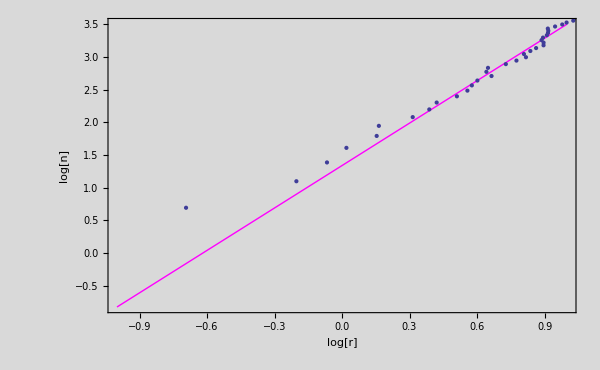

```mathematica
Clear[a,b,x]
test02=eden03[500];
logRNEqn01=logRN[findRG[test02],2]/.{a_,b_}->{a+b*x};
logRNValues01=N[Log[Drop[findRG[test02],1]]];
Plot01= Plot[logRNEqn01,{x,-1,1}, Frame -> True, ImageSize -> 600, Background -> LightGray,GridLines->Automatic,PlotStyle->Magenta,FrameLabel -> {"log[r]","log[n]","Plot of Line Based on Log[c] and d vs. actual {log[r],log[n]} Values from the Same Cluster"}];
Plot02=ListPlot[logRNValues01,Frame -> True, ImageSize -> 600, Background -> LightGray,GridLines->Automatic];
Show[Plot01,Plot02]
```

This plot shows a best-fit line drawn using the output of module logRN overlayed with the actual log[r],log[n] values from a test cluster of 500 particles (test02).  The fit is reasonably good for such a small cluster indicating that logRN is working correctly.

## Section 07: Best Value and Uncertainties for {Log[c],d} Found from a Number of Runs

Now that we have code to get us {log[c], d} values from a single run, we can take an ensemble of these runs and find a best value and uncertainty in log[c] and d.

Creating a list of {log[c],d} values for 60 Eden clusters, each 10000 units large, using r values from 5000≤n≤10000:

```mathematica
Clear[n]
data01=Monitor[Table[logRN[findRG[eden03[10000]],5000],{n,1,60}],n];
```

(Had more time, so did 130 more trials of the same thing)

```mathematica
Clear[n]
data02=Monitor[Table[logRN[findRG[eden03[10000]],5000],{n,1,130}],n];
```

Now we’ll use our statistical functions to analyze these data.  Finding the best value and uncertainty for {log[c],d}:

```mathematica
fullData=Join[data01,data02];
ave[fullData]
unc[fullData]
```

{1.68975,2.03465}

{0.00524124,0.00140861}

Thus we have found log[c] = 1.690±0.005 and d = 2.035±0.001

## Section 08: Conclusions

The goal of this notebook was to see how the number of cells in an Eden cluster, n, depends on the radius of gyration, r.  We assumed that this could be modeled by the equation n = c*r^d, where c and d are constants.  Taking the log of both sides of this equation gives log[n] = log[c]+d*log[r], showing that if we kept track of r and n and found a linear fit it would give us values for log[c] and d as the intercept and slope, respectively.

After implementing code to simulate an Eden growth model from a single starting cell, we developed modules to calculate the radius of gyration for growing values of n and to find the best-fit values of log[c] and d for specific Eden clusters.  We then ran 190 Eden model simulations and found the best value and uncertainty in log[c] and d over the range 5000≤n≤10000, which turned out to be log[c] = 1.690±0.005 and d = 2.035±0.001.

These values are reasonable if we remember that theoretically, a very large Eden cluster should be essentially circular.  The formula for the area of a circle, area = π*r^2, looks very similar to our model equation n = c*r^d, and thus if the Eden model becomes circular for large values of n we would expect to find that d ≃ 2 and log[c] ≃ log[π] ≃ 1.145.  We indeed find that our values are somewhat close (within an order of magnitude) to what we would expect, though neither is within standard error of our predictions.  This is either because the Eden model is not perfectly circular at large values or, more likely, we needed to examine larger values of n to truly see circular behavior.